```mathematica
boatDens = 1.225*(1.875/2)+710*(.125/2) ;(*Boat density (kg/m^3)*)
deckDens = 710* 0.003175 ;(*Deck area density (kg/m^2*)
mCargo = .8; (*Cargo mass (kg)*)
mMast = (π*(3/8*1/2)^2*19.685*(2.7/0.0610237))/1000; (*Mass of mast (kg)*)
comMast = {0,0,.27}; (*COM of mast (m)*)
comCargo = {0,0,.02}; (*COM of cargo (m)*)
```

```mathematica
Clear[boat,mass,com,submerged,submass,water,cob,arm]
boatFunc[n_?NumberQ,d_?NumberQ,xLen_?NumberQ,xVal_]:=Exp[Abs[y/(n*(xVal^2-xLen^2))]]+(d*(xVal^2/xLen^2))-1≤z≤d
boat= ImplicitRegion[boatFunc[16,.1,.25,x],{x,y,z}];
mass :=mass= boatDens*N[RegionMeasure[boat]]
massTot:=mass+mCargo+mMast
com:=com=(N[RegionCentroid[boat]]*mass+mCargo*comCargo+mMast*comMast)/massTot
submerged[d_,t_]:=ImplicitRegion[2*(Abs[y/2]^2+Abs[x/5]^4)<z<2&&If[t<90,z<N[Tan[t Degree]]*y+d,z>N[Tan[t Degree]]*y+d],{{x,-5,5},{y,-2,2},{z,0,2}}]
submass[d_,t_]:=1000*N[RegionMeasure[submerged[d,t]]]
water[t_]:=water[t]=FindRoot[submass[d,t]==mass,{d,-20,20}]
cob[t_]:=cob[t]=N[RegionCentroid[submerged[d,t]/.water[t]]]
arm[t_?NumberQ]:=Cross[cob[t]-com,{0,-Sin[t Degree],Cos[t Degree]}][[1]]
```

```mathematica
N[RegionMeasure[ImplicitRegion[boatFunc[17,.1,.25,x],{x,y,z}]]]
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-1+ⅇ^(1/17 Abs[Power[«2»] y])+1.6 x^2≤z≤0.1,{x,y,z}].

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-1.+2.71828^(0.0588235 Abs[Power[«2»] y])+1.6 x^2≤z≤0.1,{x,y,z}].

RegionMeasure[ImplicitRegion[-1.+2.71828^(0.0588235 Abs[y/(-0.0625+x^2)])+1.6 x^2≤z≤0.1,{x,y,z}]]

```mathematica
RegionMeasure[ImplicitRegion[-1.+2.718^(0.0588 Abs[y/(-0.0625+x^2)])+1.6 x^2≤z≤0.1,{x,y,z}]]
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-1.+2.718^(0.0588 Abs[Power[«2»] y])+1.6 x^2≤z≤0.1,{x,y,z}].

RegionMeasure[ImplicitRegion[-1.+2.718^(0.0588 Abs[y/(-0.0625+x^2)])+1.6 x^2≤z≤0.1,{x,y,z}]]

```mathematica
mass
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-1+ⅇ^(1/17 Abs[Power[«2»] y])+1.6 x^2≤z≤0.1,{x,y,z}].

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-1.+2.71828^(0.0588235 Abs[Power[«2»] y])+1.6 x^2≤z≤0.1,{x,y,z}].

45.5234 RegionMeasure[ImplicitRegion[-1.+2.71828^(0.0588235 Abs[y/(-0.0625+x^2)])+1.6 x^2≤z≤0.1,{x,y,z}]]

```mathematica
1.225*(1.875/2)+710*(.125/2)
```

45.5234

```mathematica
prisCoeff:=N[RegionMeasure[submerged[d,0]/.water[0]]]/(N[RegionMeasure[ImplicitRegion[boatFunc[.02,4,10,0],{y,z}]]*2(RegionBounds[boat][[1,2]]-RegionBounds[boat][[1,1]])])
```

```mathematica
prisCoeff
```

0.00153438

```mathematica
RegionBounds[boat]
```

{{-9.83321,9.7187},{-64.3775,64.3775},{-4.53324×10^-9,4.}}

```mathematica
RegionBounds[boat]
```

RegionBounds::reg: 5 ImplicitRegion[ⅇ^(2.5 Abs[Times[«2»]])+1/6 (-4+x^2)≤z≤1,{x,y,z}] is not a correctly specified region.

RegionBounds[5 ImplicitRegion[ⅇ^(2.5 Abs[y/(-4+x^2)])+1/6 (-4+x^2)≤z≤1,{x,y,z}]]

```mathematica
boat
```

ImplicitRegion[ⅇ^(2.5 Abs[y/(-100+x^2)])+1/6 (-100+x^2)≤z≤10,{x,y,z}]

```mathematica
RegionPlot3D[boatFunc[17,.1,.25,x],{x,-.249,.249},{y,-.1,.1},{z,0,.1},AxesLabel->Automatic,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
points = Map[arm,Range[0,180,20]]
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[2 (1/625 Abs[«1»]^4+1/4 Abs[«1»]^2)<z<2&&z<0.+d&&-5≤x≤5&&-2≤y≤2&&0≤z≤2,{x,y,z}].

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[2. (0.0016 Abs[«1»]^4+0.25 Abs[«1»]^2)<z<2.&&z<0.+d&&-5.≤x≤5.&&-2.≤y≤2.&&0.≤z≤2.,{x,y,z}].

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[2 (1/625 Abs[«1»]^4+1/4 Abs[«1»]^2)<z<2&&z<d+0.36397 y&&-5≤x≤5&&-2≤y≤2&&0≤z≤2,{x,y,z}].

General::stop: Further output of RegionMeasure::nmet will be suppressed during this calculation.

{0.,0.118057,0.405587,1.44344,1.35439,0.76315,0.055926,-0.659214,-1.27682,1.70177×10^-18}

```mathematica
angles = Range[0,180,20]
newPoints = Transpose[{angles,points}]
```

{0,20,40,60,80,100,120,140,160,180}

{{0,0.},{20,0.118057},{40,0.405587},{60,1.44344},{80,1.35439},{100,0.76315},{120,0.055926},{140,-0.659214},{160,-1.27682},{180,1.70177×10^-18}}

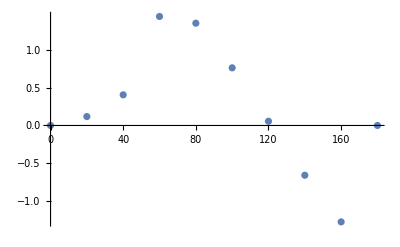

```mathematica
ListPlot[newPoints]
```

```mathematica
boatFunc[n_,d_,xVal_]:=Exp[Abs[y/(n*(xVal^2-4))]]+(xVal^2-4)/6≤z≤d
RegionMeasure[ImplicitRegion[boatFunc[.4,1,x],{x,y,z}]]
```

7.99093